```mathematica
pxy=PDF[MultinormalDistribution[{(θx1+θx2)/2,(θy1+θy2)/2},{{λ,0},{0,λ}}],{x,y}]
```

ⅇ^(1/2 (-((x+1/2 (-θx1-θx2)) (2 x-θx1-θx2))/(2 λ)-((y+1/2 (-θy1-θy2)) (2 y-θy1-θy2))/(2 λ)))/(2 π √(λ^2))

```mathematica
wxy1=2 π PDF[MultinormalDistribution[{θx1,θy1},{{1,0},{0,1}}],{x,y}]
wxy2=2 π PDF[MultinormalDistribution[{θx2,θy2},{{1,0},{0,1}}],{x,y}]
```

ⅇ^(1/2 (-(x-θx1)^2-(y-θy1)^2))

ⅇ^(1/2 (-(x-θx2)^2-(y-θy2)^2))

```mathematica
Integrate[wxy1 PDF[MultinormalDistribution[{θx1,θy1},{{λ,0},{0,λ}}],{x,y}]/.θx1->0/.θy1->0,{x,-∞,∞},{y,-∞,∞},Assumptions->λ>0]
varload=-Log[%]
```

1/(1+λ)

-Log[1/(1+λ)]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

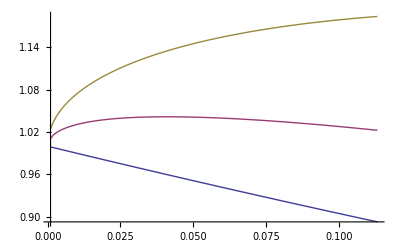

```mathematica
θx1=1;
θy1=0;
θx2=Cos[θ*π/180];
θy2=Sin[θ*π/180];
θs={0,60,180};nθ=Length[θs];

novar=(wxy1/.x->(θx1+θx2)/2/.y->(θy1+θy2)/2);

Table[{varload,NIntegrate[Max[wxy1,wxy2]pxy/.θ->θs[[i]],{x,-∞,∞},{y,-∞,∞}]/novar/.θ->θs[[i]]},{i,Length[θs]},{λ,10^-3,0.12,0.001}];
ListPlot[%,Joined->True,PlotRange->All]



Clear[θx1,θx2,θy1,θy2,θs,θ]
```